```mathematica
Nl = UnitConvert[(183 * StarData["Sun","Mass"])/Quantity[1,"pc^2"],"g/cm^2"]
n =UnitConvert[ Nl/(1.37 ParticleData["Proton","Mass"]),"1/pc^2"]
```

0.03821742

1.58798×10^59

```mathematica
λ= UnitConvert[((n π)/(1.37 ParticleData["Proton","Mass"]))^(-1/2),"cm"]
M = n * π λ^2
ρ = M/(π λ^2)
```

4.36871×10^-12

2.29149×10^-24

0.0382174

```mathematica
Remove["Global`*"]
a=Mdot/(4π)((G Ms)/R^3)^(-1/2);
ρ=b(r/R)^(-3/2)(1+mu/mu0)^(-1/2)(mu/mu0+(2 mu0^2 R)/r)^-1/.Solve[mu0^3+mu0(r/R-1)-mu (r/R) ==0,mu0][[1]]/.mu->Cos[θ]/.r->r R/.b->1;
```

```mathematica
2NIntegrate[ρ r^2 Sin[θ],{r,0,1},{ϕ,0,2π},{θ,0,π/2}]/(2NIntegrate[r^2 Sin[θ],{r,0,1},{ϕ,0,2π},{θ,0,π/2}])
```

0.697331

```mathematica
Quantity[1,"kg/s"](Quantity[1,"G"]Quantity[1,"kg"]/Quantity[1,"m^3"])^(-1/2)//UnitSimplify
```

122000.

```mathematica
Remove["Global`*"]
ρ=b(r/R)^(-3/2)(1+mu/mu0)^(-1/2)(mu/mu0+(2 mu0^2 R)/r)^-1/.Solve[mu0^3+mu0(r/R-1)-mu (r/R) ==0,mu0][[1]]/.mu->Cos[θ]/.r->r R/.b->1;
g[n_]:= 2NIntegrate[ρ r^2 Sin[θ],{r,0,1},{ϕ,0,2π},{θ,n Degree,π/2}]
f=Table[{x,g[x]},{x,0,90}];
```

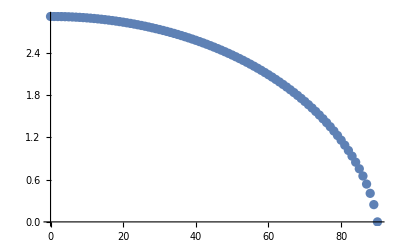

```mathematica
ListPlot[f]
```

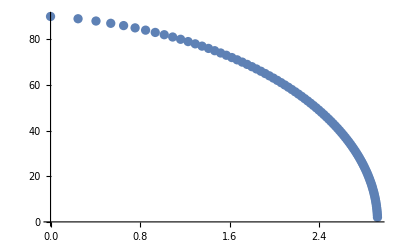

```mathematica
f2=Table[{g[x],x},{x,2,90}];
ListPlot[f2]
```

```mathematica
sol1 = FindFit[f2,b/(x-a)^n,{b,a,n},x]
sol2 = FindFit[f,(b x)/(x-a)^n,{{b,4.5},{a,0.5},{n,.13}},x]
```

{b→4.05501,a→-0.485486,n→1.13034}

FindFit::nrlnum: The function value {-2.92098 + 0.\ ⅈ, -2.58881 - 0.170344\ ⅈ, -2.18673 - 0.376359\ ⅈ, -1.25927 - 0.851764\ ⅈ, -1.23371 + 0.\ ⅈ, « 41 », 8.39755  + 0.\ ⅈ, 8.617  + 0.\ ⅈ, 8.83648  + 0.\ ⅈ, 9.05601  + 0.\ ⅈ, « 41 »} is not a list of real numbers with dimensions {91} at {b, a, n} = {0.41642, 3.07011, 0.150913}.

{b→0.41642,a→3.07011,n→0.150913}

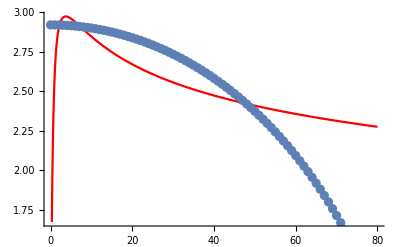

```mathematica
Show[Plot[(b x)/(x-a)^n/.sol1,{x,0,80},PlotStyle->Red],ListPlot[f]]
```